```mathematica
(*Question 2a&b*)
ni=2((kB*T)/(2π*hbar^2))^(3/2)*(me*mh)^(3/4)*Exp[-Eg/(2*kB*T)];
FullSimplify[kB*T*Log[(Nd*Na)/ni^2]]
```

kB T Log[(2 ⅇ^(Eg/(kB T)) hbar^6 Na Nd π^3)/(kB^3 (me mh)^(3/2) T^3)]

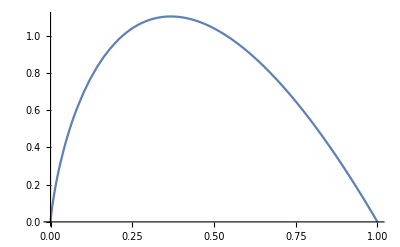

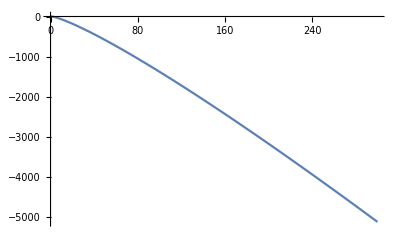

```mathematica
Plot[-T*Log[T^3],{T,0,1}]
Plot[-T*Log[T^3],{T,0,300}]
```

```mathematica
(4.1*10^-21)*Log[((4*10^17)(8*10^15))/((1.1*10^10)^2)]
(4.1*10^-21)*Log[((4*10^17)(8*10^15))/((1.1*10^10)^2)]/(1.602*10^-19)
```

1.26715×10^-19

0.790981

```mathematica
(*Question 2c*)
(8*10^15)/(4*10^17)
```

1/50

```mathematica
(*Question 2d*)
(((4*10^17)/(8*10^15))/(4*10^17+8*10^15)*((2*11.68*(8.85*10^-14)*(0.79098))/(1.602*10^-19)))^(1/2)
(((4*10^17)/(8*10^15))/(4*10^17+8*10^15)*((2*11.68*(8.85*10^-14)*(0.79098))/(1.602*10^-19)))^(1/2)/50
51*(((4*10^17)/(8*10^15))/(4*10^17+8*10^15)*((2*11.68*(8.85*10^-14)*(0.79098))/(1.602*10^-19)))^(1/2)/50
```

0.0000353683

7.07366×10^-7

0.0000360757

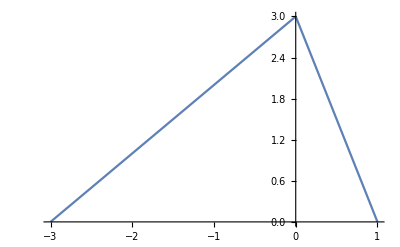

```mathematica
(*Question 3*)
Na=3*Nd;
dp=1;
dn=3;
p1=Plot[((Nd*dn)/(e0*er)(x+dn))/(Na/(e0*er)),{x,-dn,0}];
p2=Plot[((Na*dp)/(e0*er)(dp-x))/(Nd/(e0*er)),{x,0,dp}];
Show[p1,p2,PlotRange->All]
```